```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zakk/Desktop/ISTAustria/AngulonDiagMC/Analysis

```mathematica
MyImport[fname_]:=Cases[Import[fname,"Table"],{_?NumberQ,___}];
```

```mathematica
{minτ,maxτ}={7,14};
```

```mathematica
{minτ,maxτ}={3,8};
```

```mathematica
prefixList={"m10","m9","m8","m7","m6","m5","m4","m3","m2","m1","0","1","2","3","4","5"};
```

```mathematica
readμ[fname_]:=ToExpression@First@With[{txt=ReadList[fname,String]},Flatten@StringCases[txt,"# Chemical potential: "~~(x:NumberString)->ToExpression@x]]
```

```mathematica
readlogn[fname_]:=ToExpression@First@With[{txt=ReadList[fname,String]},Flatten@StringCases[txt,"# Potential parameters: (logn) = ("~~(x:NumberString)->ToExpression@x]]
```

```mathematica
readavgorder[prefix_]:=ToExpression@First@With[{txt=ReadList[prefix,String]},Flatten@StringCases[txt,"# Average order: "~~(x:NumberString)->ToExpression@x]]
```

```mathematica
μsj0=Transpose[{readlogn["j0/test"<>#<>".dat"]&/@prefixList,readμ["j0/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
avgordersj0=Transpose[{readlogn["j0/test"<>#<>".dat"]&/@prefixList,readavgorder["j0/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
μsj1=Transpose[{readlogn["j1/test"<>#<>".dat"]&/@prefixList,readμ["j1/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
μ[j_,logn_]:=Switch[j,0,First[Select[μsj0,#[[1]]==logn&]][[2]],1,First[Select[μsj1,#[[1]]==logn&]][[2]],2,First[Select[μsj2,#[[1]]==logn&]][[2]]];
```

```mathematica
avgorder[logn_]:=Switch[j,0,First[Select[avgordersj0,#[[1]]==logn&]][[2]],1,First[Select[avgordersj1,#[[1]]==logn&]][[2]],2,First[Select[avgordersj2,#[[1]]==logn&]][[2]]]
```

```mathematica
cListj0=Transpose[{prefixList,readlogn["j0/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
dListj0={#[[2]],MyImport["j0/test"<>#[[1]]<>".dat"]}&/@cList;
```

```mathematica
cListj1=Transpose[{prefixList,readlogn["j1/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
dListj1={#[[2]],MyImport["j1/test"<>#[[1]]<>".dat"]}&/@cList;
```

```mathematica
cListj2=Transpose[{prefixList,readlogn["j2/test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
dListj2={#[[2]],MyImport["j2/test"<>#[[1]]<>".dat"]}&/@cList;
```

```mathematica
GetSingleList[j_,logn_]:=First[Select[Switch[j,0,dListj0,1,dListj1,2,dListj2],#[[1]]==logn&]][[2]]
```

```mathematica
GetRawParameters[j_,logn_]:=With[{data=GetSingleList[j,logn]},With[{refinedData=Select[data,minτ<#[[1]]<maxτ&]},NonlinearModelFit[{#[[1]],Log[#[[2]]]}&/@refinedData,q+m *x,{q,m},x]]]["BestFitParameters"]
```

```mathematica
GetParameters[j_,logn_]:={z->Exp[q],En->μ[j,logn]-m}/.GetRawParameters[j,logn]
```

```mathematica
fDataj0=With[{logns=#[[2]]&/@cList},{#,GetParameters[0,#],avgorder[0,#]}&/@logns];
```

```mathematica
GetParameters[1,-10]
```

{z→0.023257,En→1.01418}

```mathematica
fDataj1=With[{logns=#[[2]]&/@cListj1},{#,GetParameters[1,#],avgorder[1,#]}&/@logns];
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ReplaceAll::reps: {NonlinearModelFit[{{3.0125,-4.88383},{3.0375,-4.80033},{3.0625,-4.95586},{3.0875,-4.84928},{3.1125,-5.01963},«41»,{4.1625,-6.55218},{4.1875,-6.6271},{4.2125,-6.0373},{4.2375,-6.66481},«150»},q+m x,{q,m},x][Bes…ters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ReplaceAll::reps: {NonlinearModelFit[{{3.0125,-6.82341},{3.0375,-6.76279},{3.0625,-6.84666},{3.0875,-6.84197},{3.1125,-6.95066},«41»,{4.1625,-8.41735},{4.1875,-8.52724},{4.2125,-8.22452},{4.2375,-8.43102},«150»},q+m x,{q,m},x][Best…ters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{3.0125,-4.88383},{3.0375,-4.80033},{3.0625,-4.95586},{3.0875,-4.84928},{3.1125,-5.01963},«41»,{4.1625,-6.55218},{4.1875,-6.6271},{4.2125,-6.0373},{4.2375,-6.66481},«150»},q+m x,{q,m},x][Bes…ters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
fDataj1
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ReplaceAll::reps: {NonlinearModelFit[{{3.0125,-4.88383},{3.0375,-4.80033},{3.0625,-4.95586},{3.0875,-4.84928},{3.1125,-5.01963},«41»,{4.1625,-6.55218},{4.1875,-6.6271},{4.2125,-6.0373},{4.2375,-6.66481},«150»},q+m x,{q,m},x][Bes…ters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

ReplaceAll::reps: {NonlinearModelFit[{{3.0125,-6.82341},{3.0375,-6.76279},{3.0625,-6.84666},{3.0875,-6.84197},{3.1125,-6.95066},«41»,{4.1625,-8.41735},{4.1875,-8.52724},{4.2125,-8.22452},{4.2375,-8.43102},«150»},q+m x,{q,m},x][Best…ters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{-10.,{z→0.023257,En→1.01418},avgorder[1,-10.]},{-9.,{z→0.00181912,En→0.345815},avgorder[1,-9.]},{-8.,{z→0.00251355,En→0.295298},avgorder[1,-8.]},{-7.,{z→(-nan)^1.,En→1.99756+8.42171×10^-17 Log[-nan]},avgorder[1,-7.]},{-6.,{z→ⅇ^q,En→-0.312012-m}/.NonlinearModelFit[{{3.0125,-4.88383},{3.0375,-4.80033},{3.0625,-4.95586},{3.0875,-4.84928},{3.1125,-5.01963},{3.1375,-4.95161},{3.1625,-5.23422},{3.1875,-5.07134},{3.2125,-5.10654},{3.2375,-5.10357},{3.2625,-5.31323},{3.2875,-5.25373},{3.3125,-5.22395},{3.3375,-5.37132},{3.3625,-5.47816},{3.3875,-5.44265},{3.4125,-5.63128},{3.4375,-5.52271},{3.4625,-5.58334},{3.4875,-5.5409},{3.5125,-5.68486},{3.5375,-5.63799},{3.5625,-5.62599},{3.5875,-5.79196},{3.6125,-5.92269},{3.6375,-5.69195},{3.6625,-5.76258},{3.6875,-5.53937},{3.7125,-5.44682},{3.7375,-5.61111},{3.7625,-5.55812},{3.7875,-5.45684},{3.8125,-5.83207},{3.8375,-5.88064},{3.8625,-5.79196},{3.8875,-5.50019},{3.9125,-5.80184},{3.9375,-6.01494},{3.9625,-6.4478},{3.9875,-6.24816},{4.0125,-5.94802},{4.0375,-6.26065},{4.0625,-6.0606},{4.0875,-6.08402},{4.1125,-6.2733},{4.1375,-6.11657},{4.1625,-6.55218},{4.1875,-6.6271},{4.2125,-6.0373},{4.2375,-6.66481},{4.2625,-6.59587},{4.2875,-6.2733},{4.3125,-6.57845},{4.3375,-6.31941},{4.3625,-6.49896},{4.3875,-6.97925},{4.4125,-6.86278},{4.4375,-6.70809},{4.4625,-6.55218},{4.4875,-6.80701},{4.5125,-7.04702},{4.5375,-6.96644},{4.5625,-7.19544},{4.5875,-6.6271},{4.6125,-7.2211},{4.6375,-6.87432},{4.6625,-6.89287},{4.6875,-7.21292},{4.7125,-6.72294},{4.7375,-7.42192},{4.7625,-6.66481},{4.7875,-8.18789},{4.8125,-6.9168},{4.8375,-7.2211},{4.8625,-7.78242},{4.8875,-7.2716},{4.9125,-7.52765},{4.9375,-7.97197},{4.9625,-7.33393},{4.9875,-8.08541},{5.0125,-7.21292},{5.0375,-7.1111},{5.0625,-7.21292},{5.0875,-7.51656},{5.1125,-6.96644},{5.1375,-7.24603},{5.1625,-6.92287},{5.1875,-8.02861},{5.2125,-7.87271},{5.2375,-7.87271},{5.2625,-7.17172},{5.2875,-7.04702},{5.3125,-8.35168},{5.3375,-8.06612+3.14159 ⅈ},{5.3625,-7.55021},{5.3875,-8.97132},{5.4125,-7.82655},{5.4375,-8.40386},{5.4625,-7.85709},{5.4875,-10.9251+3.14159 ⅈ},{5.5125,-7.69962},{5.5375,-8.32657},{5.5625,-8.40386},{5.5875,-7.93777},{5.6125,-7.42192},{5.6375,-8.45892},{5.6625,-10.9251},{5.6875,-9.01972},{5.7125,Indeterminate},{5.7375,-8.01038},{5.7625,-7.38096},{5.7875,-7.2211},{5.8125,-10.6375+3.14159 ⅈ},{5.8375,-7.6459},{5.8625,-7.72647},{5.8875,-9.2408},{5.9125,-8.79823},{5.9375,-9.52505},{5.9625,-9.30465+3.14159 ⅈ},{5.9875,-8.92516+3.14159 ⅈ},{6.0125,-8.01038},{6.0375,-7.87271},{6.0625,-9.82653},{6.0875,-8.92516},{6.1125,-8.75926},{6.1375,-8.92516},{6.1625,-5.72297},{6.1875,-5.70089},{6.2125,-5.80184},{6.2375,-6.01494},{6.2625,-6.1904},{6.2875,-6.24198},{6.3125,-5.78967},{6.3375,-6.66011},{6.3625,-7.07499},{6.3875,-6.59587},{6.4125,-6.48707},{6.4375,-6.21111},{6.4625,-7.57329},{6.4875,-6.35675},{6.5125,-7.47339},{6.5375,-6.82341},{6.5625,-6.59587},{6.5875,-6.71796},{6.6125,-9.82653+3.14159 ⅈ},{6.6375,-9.82653+3.14159 ⅈ},{6.6625,-7.21292},{6.6875,-7.45248},{6.7125,-7.88858+3.14159 ⅈ},{6.7375,-6.87432},{6.7625,-7.63343},{6.7875,-7.33393},{6.8125,-6.58712},{6.8375,-8.04719},{6.8625,-8.18789},{6.8875,-7.69962+3.14159 ⅈ},{6.9125,-8.48763},{6.9375,-8.08541},{6.9625,-9.37286},{6.9875,-8.01038},{7.0125,-6.9168},{7.0375,-7.01869+3.14159 ⅈ},{7.0625,-8.35168+3.14159 ⅈ},{7.0875,-6.46757},{7.1125,-6.64539},{7.1375,-7.10377},{7.1625,-6.8988},{7.1875,-7.51656},{7.2125,-7.99246},{7.2375,-7.25448},{7.2625,-9.18078},{7.2875,-8.20971},{7.3125,-7.92111},{7.3375,-8.72176+3.14159 ⅈ},{7.3625,-7.14095},{7.3875,-7.18747},{7.4125,-8.20971},{7.4375,-7.2211+3.14159 ⅈ},{7.4625,-7.07499},{7.4875,-10.4143+3.14159 ⅈ},{7.5125,-7.31572+3.14159 ⅈ},{7.5375,-8.02861+3.14159 ⅈ},{7.5625,-7.59691},{7.5875,-6.8345},{7.6125,-10.6375+3.14159 ⅈ},{7.6375,-8.30208+3.14159 ⅈ},{7.6625,-7.01201},{7.6875,-7.97197},{7.7125,-10.9251+3.14159 ⅈ},{7.7375,Indeterminate},{7.7625,-7.53887+3.14159 ⅈ},{7.7875,-8.18789+3.14159 ⅈ},{7.8125,-8.16654+3.14159 ⅈ},{7.8375,-7.22934+3.14159 ⅈ},{7.8625,-9.62586+3.14159 ⅈ},{7.8875,-8.06612},{7.9125,-8.14563},{7.9375,-8.04719+3.14159 ⅈ},{7.9625,-7.78242+3.14159 ⅈ},{7.9875,-7.0965+3.14159 ⅈ}},q+m x,{q,m},x][BestFitParameters],avgorder[1,-6.]},{-5.,{z→0.00833311-0.0532037 ⅈ,En→-0.158628-0.365879 ⅈ},avgorder[1,-5.]},{-4.,{z→ⅇ^q,En→-2.06006-m}/.NonlinearModelFit[{{3.0125,-6.82341},{3.0375,-6.76279},{3.0625,-6.84666},{3.0875,-6.84197},{3.1125,-6.95066},{3.1375,-6.95171},{3.1625,-7.217},{3.1875,-6.87917},{3.2125,-7.02317},{3.2375,-7.05278},{3.2625,-7.03559},{3.2875,-7.07263},{3.3125,-6.9538},{3.3375,-7.21836},{3.3625,-7.43032},{3.3875,-7.28172},{3.4125,-7.25731},{3.4375,-7.37138},{3.4625,-7.20886},{3.4875,-7.48223},{3.5125,-7.587},{3.5375,-7.67995},{3.5625,-7.53511},{3.5875,-7.88592},{3.6125,-7.71744},{3.6375,-7.76578},{3.6625,-8.01945},{3.6875,-7.95472},{3.7125,-7.76814},{3.7375,-8.14563},{3.7625,-8.00437},{3.7875,-8.05977},{3.8125,-8.05661},{3.8375,-8.48763},{3.8625,-8.03786},{3.8875,-7.92387},{3.9125,-8.1736},{3.9375,-7.81657},{3.9625,-7.94339},{3.9875,-7.99246},{4.0125,-8.29405},{4.0375,-7.97487},{4.0625,-8.28212},{4.0875,-8.35168},{4.1125,-8.46365},{4.1375,-7.86487},{4.1625,-8.41735},{4.1875,-8.52724},{4.2125,-8.22452},{4.2375,-8.43102},{4.2625,-8.68561},{4.2875,-8.90286},{4.3125,-8.62255},{4.3375,-8.61701},{4.3625,-8.9557},{4.3875,-8.75292},{4.4125,-8.54765},{4.4375,-9.4588},{4.4625,-8.75292},{4.4875,-8.78507},{4.5125,-8.89553},{4.5375,-9.3157},{4.5625,-9.11503},{4.5875,-9.48478},{4.6125,-9.01972},{4.6375,-9.51145},{4.6625,-8.94031},{4.6875,-9.07931},{4.7125,-9.3157},{4.7375,-9.19054},{4.7625,-13.8155},{4.7875,-10.0088},{4.8125,-9.13338},{4.8375,-11.3306},{4.8625,-9.596},{4.8875,-8.47797},{4.9125,-10.5197},{4.9375,-9.79016},{4.9625,-9.32687},{4.9875,-9.10598},{5.0125,-11.1765+3.14159 ⅈ},{5.0375,-13.1224},{5.0625,-9.42106},{5.0875,-10.6375+3.14159 ⅈ},{5.1125,-9.3157},{5.1375,-9.2408},{5.1625,-9.84522},{5.1875,-9.19054},{5.2125,-9.15207},{5.2375,-10.2046},{5.2625,-9.44606},{5.2875,-9.75507},{5.3125,-9.22039},{5.3375,-10.4833+3.14159 ⅈ},{5.3625,-9.56702},{5.3875,-9.96536},{5.4125,-10.5574},{5.4375,-9.51145},{5.4625,-9.18078+3.14159 ⅈ},{5.4875,-9.43348},{5.5125,-9.48478},{5.5375,-9.67238},{5.5625,-9.79016},{5.5875,-11.1075},{5.6125,-11.3306},{5.6375,-10.3815},{5.6625,-10.0543},{5.6875,-10.1779+3.14159 ⅈ},{5.7125,-10.319},{5.7375,-9.64112},{5.7625,-11.3306},{5.7875,-10.2046+3.14159 ⅈ},{5.8125,-9.15207},{5.8375,-9.42106},{5.8625,-12.7169+3.14159 ⅈ},{5.8875,-10.4482},{5.9125,-9.53884},{5.9375,-10.5574},{5.9625,-10.2046},{5.9875,-9.86427},{6.0125,-9.88368+3.14159 ⅈ},{6.0375,-10.319+3.14159 ⅈ},{6.0625,-10.771+3.14159 ⅈ},{6.0875,-10.2892},{6.1125,-9.5814},{6.1375,-8.8183},{6.1625,-10.3815},{6.1875,-9.28291},{6.2125,-9.96536+3.14159 ⅈ},{6.2375,-10.2046},{6.2625,-10.1266},{6.2875,-9.39667},{6.3125,-9.53884},{6.3375,-10.2046},{6.3625,-9.90349+3.14159 ⅈ},{6.3875,-9.55283},{6.4125,-10.0313},{6.4375,-10.5574},{6.4625,-10.319},{6.4875,-10.2046+3.14159 ⅈ},{6.5125,-11.1075},{6.5375,-10.5966+3.14159 ⅈ},{6.5625,-11.1075},{6.5875,-11.7361},{6.6125,-10.1019},{6.6375,-10.3815+3.14159 ⅈ},{6.6625,-12.4292},{6.6875,-10.1019},{6.7125,-10.4482},{6.7375,-10.7245+3.14159 ⅈ},{6.7625,Indeterminate},{6.7875,-9.94431},{6.8125,-10.0313+3.14159 ⅈ},{6.8375,-9.73797},{6.8625,-11.2506+3.14159 ⅈ},{6.8875,-13.8155},{6.9125,-9.68838},{6.9375,-9.33817+3.14159 ⅈ},{6.9625,-9.92369},{6.9875,-12.4292+3.14159 ⅈ},{7.0125,-12.4292+3.14159 ⅈ},{7.0375,-9.29372+3.14159 ⅈ},{7.0625,-11.7361+3.14159 ⅈ},{7.0875,-12.2061+3.14159 ⅈ},{7.1125,-10.6375},{7.1375,-9.56702},{7.1625,-9.92369},{7.1875,-8.31018},{7.2125,-8.72176},{7.2375,-8.01339},{7.2625,-9.16155},{7.2875,-8.76565},{7.3125,-8.58976},{7.3375,-9.20039},{7.3625,-8.25099},{7.3875,-12.7169+3.14159 ⅈ},{7.4125,-8.93271},{7.4375,-8.47318},{7.4625,-10.0313+3.14159 ⅈ},{7.4875,-10.8198},{7.5125,-8.47318},{7.5375,-8.8457},{7.5625,-9.90349},{7.5875,-8.39056},{7.6125,-8.65072},{7.6375,-8.44023},{7.6625,-10.9823},{7.6875,-9.44606},{7.7125,-8.4925},{7.7375,-8.52724},{7.7625,-10.7245},{7.7875,-9.02802},{7.8125,-12.0238},{7.8375,-8.58976},{7.8625,-9.38469},{7.8875,-12.4292},{7.9125,-9.17112+3.14159 ⅈ},{7.9375,-9.25116},{7.9625,-9.73797+3.14159 ⅈ},{7.9875,-10.1019+3.14159 ⅈ}},q+m x,{q,m},x][BestFitParameters],avgorder[1,-4.]},{-3.,{z→0.00106459-0.00152323 ⅈ,En→-2.19844-0.311779 ⅈ},avgorder[1,-3.]},{-2.,{z→0.00808036-0.0079398 ⅈ,En→-2.0769-0.281148 ⅈ},avgorder[1,-2.]},{-1.,{z→0.301182-0.0426535 ⅈ,En→-1.80314-0.031291 ⅈ},avgorder[1,-1.]},{0.,{z→0.424766,En→-2.00908},avgorder[1,0.]},{1.,{z→0.575356,En→-2.16318},avgorder[1,1.]},{2.,{z→0.745905,En→-2.27035},avgorder[1,2.]},{3.,{z→0.803694,En→-2.36788},avgorder[1,3.]},{4.,{z→0.785186,En→-2.45735},avgorder[1,4.]},{5.,{z→0.836615,En→-2.52191},avgorder[1,5.]}}

```mathematica
dmcP1=ListPlot[{#[[1]],En/.#[[2]]}&/@fDataj1]
```

ListPlot::lpn: cList1 is not a list of numbers or pairs of numbers.

ListPlot[cList1]

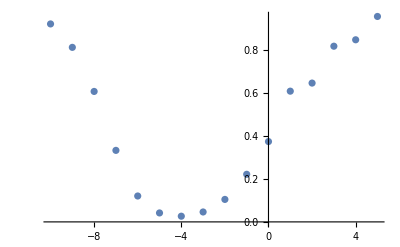

```mathematica
dmcP1=ListPlot[{#[[1]],z/.#[[2]]}&/@fDataj0]
```

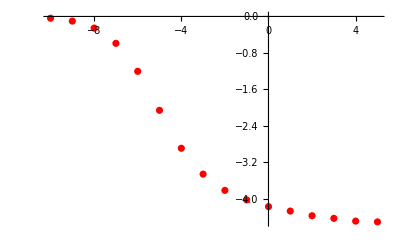

```mathematica
dmcP2=ListPlot[{#[[1]],En/.#[[2]]}&/@fData,PlotStyle->Red]
```

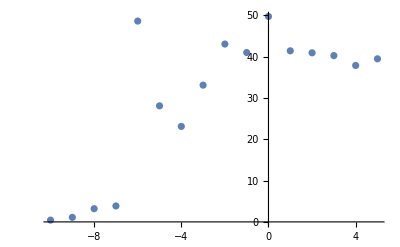

```mathematica
dmcP3=ListPlot[{#[[1]],#[[3]]}&/@fData]
```

Here we need to load the notebook SelfEnergies.nb

```mathematica
<<SelfEnergies.m
```

```mathematica
V[λ_,k_,{n_}]:=U[λ,k,{n}]Sqrt[(2*λ+1)/(4*π)]
```

```mathematica
Edef[n_]:=-NIntegrate[V[0,k,{n}]^2/ωk[k,{n}],{k,0,Infinity}]-NIntegrate[V[1,k,{n}]^2/ωk[k,{n}],{k,0,Infinity}]
```

```mathematica
scResult=ListPlot[Table[{logn,Edef[Exp[logn]]},{logn,-15,5,0.1}],Joined->True,PlotStyle->{Dashed,Red}];
```

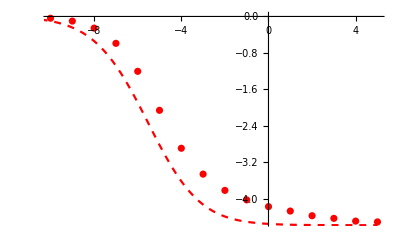

```mathematica
Show[dmcP2,scResult]
```

```mathematica
dataSpectral=Sort@Import["spectral1st.dat"];
```

```mathematica
dataSpectralSparse=Select[dataSpectral,(Abs[FractionalPart[10*#[[1]]]]<0.01)&&(Abs[FractionalPart[10*#[[2]]]]<0.01)&];
```

```mathematica
p1=ListDensityPlot[{#[[1]],#[[2]],1/(0.0001+#[[3]])^((1/10))}&/@dataSpectralSparse];
```

```mathematica
Show[p1,dmcP2,scResult]
```

-Graphics-